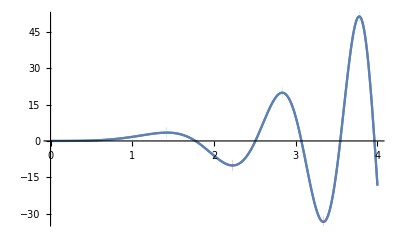

```mathematica
funkcja:=x Sin[x^2]*(2^x)
rozmiar:=4
Show[
Plot[funkcja,{x,0,rozmiar},Exclusions->{{D[funkcja,x]==0,D[funkcja,{x,2}]≤0}},ExclusionsStyle->Directive[Thickness[0.02],Green]],
Plot[funkcja,{x,0,rozmiar},Exclusions->{{D[funkcja,x]==0,D[funkcja,{x,2}]≥0}},ExclusionsStyle->Directive[Thickness[0.02],Red]]
]
```

```mathematica
1
```